# Hydra torsional stiffness

Experimental points acquired {mass (kg), displacement (mm)}

```mathematica
data={{1.28+4.72,8.7},
{1.28+9.70,17.5},
{1.28+6.46+1.30,13.6},
{1.28+6.46+5.32,21.6},
{1.28+16.52,28.3},
{1.28+16.52+6.46,43.3},
{1.28+16.52+9.70,48},
{1.28+16.52+4.72,43.9},
{1.28+6.46+6.46,26.1},
{6.46+6.46+4.72+1.28,33.7},
{1.28+16.52+9.70+6.46,59.7},
{1.28+16.52+9.70+6.46+6.46,69},
{1.28+16.52+9.70+3.3,55}};
```

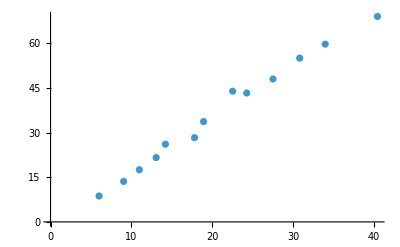

```mathematica
ListPlot[data]
```

Linear interpolation

```mathematica
model=LinearModelFit[data,x,x,IncludeConstantBasis->False]
```

FittedModel[…]

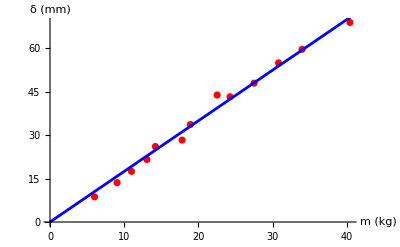

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[model[x],{x,0,1000},PlotStyle->Blue],AxesLabel -> {"m (kg)", "δ (mm)"}]
```

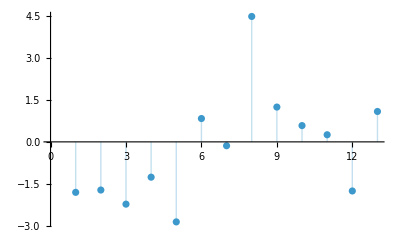

```mathematica
ListPlot[model["FitResiduals"],Filling->Axis]
```

Distance where the masses are applied:

```mathematica
l=1.30; (*m*)
```

Distance between the laser and the wall

```mathematica
L=15220;(*mm*)
```

Torque applied to the chassis

```mathematica
T=l*m*9.81
```

12.753 m

Displacement of the laser dot

```mathematica
δ = model[m](*mm*)
```

1.75046 m

Angle of rotation

```mathematica
θ=ArcTan[δ/L]*180/π;(*°*)
```

Tosional stiffness

```mathematica
K=Simplify[T/θ] (*Nm/°*)
```

(0.222582 m)/ArcTan[0.000115011 m]

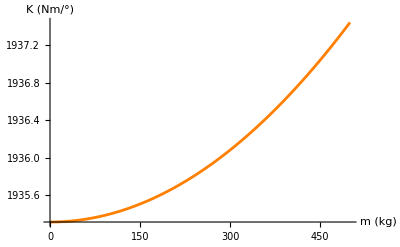

```mathematica
Plot[K,{m,0,500},PlotStyle->Orange,AxesLabel -> {"m (kg)", "K (Nm/°)"}]
```

## Simulation comparison

```mathematica
Ksim=1988.11;(*Nm/°*)
```

With a torque applied of 117Nm, equivalent to a mass of:

```mathematica
msim=117/(l*9.81)
```

9.17431

```mathematica
K/.m->msim
```

1935.31

We have a difference in percentege of:

```mathematica
100-(K/.m->msim)/Ksim*100
```

2.65562